# Mathematica tutorial

### Author

Shivam Verma

Research Scholar, Dept . of Physics
RKMVERI, Belur Campus

10 May 2022

Email address : shivam .59910103@gmail.com

## Basic concepts

```mathematica
2 +3
```

5

key to Evaluation: Shift+Enter

To comment selected text : Alt + /

Use palette (basic math assistant) in top bar for information on other basic operations like sqrt (ctrl+2)

```mathematica
√12//N/.{Precision}
```

```mathematica
N[√12]
```

3.4641

```mathematica
N[π,8]
```

3.1415927

```mathematica
π//N
```

3.14159

```mathematica
π//N
```

3.14159

let’s say, you want special characters, then use 
esc+(short for/latex form of the symbol)+esc, it will give you options as soon as you start typing

```mathematica
N[π]
```

3.14159

```mathematica
π//N
```

3.14159

```mathematica
(*Precision of a number*)
```

Things in blue are unassigned quantity
where as black represents an already assigned quantity

```mathematica
η
```

η

to comment a part of cell or the entire cell itself, select the cell and press alt + /

## List

```mathematica
(*One way*)
a = List[1,2,3,4]
```

{1,2,3,4}

```mathematica
(*Second way*)
b = {1,2,3,4}
```

{1,2,3,4}

```mathematica
Join[{{a,b}}]//MatrixForm
```

((1
2
3
4) | (1
2
3
4))

```mathematica
a==b
```

True

```mathematica
(*check what is going on within*)
```

```mathematica
FullForm[b]
```

List[1,2,3,4]

```mathematica
(*combine two lists*)
```

```mathematica
c = {2,5,7,89}
```

{2,5,7,89}

```mathematica
Join[a,b]
```

{1,2,3,4,1,2,3,4}

```mathematica
Join[{a,b}]
```

(1 | 2 | 3 | 4
1 | 2 | 3 | 4)

```mathematica
d={5,89,64,21}
```

{5,89,64,21}

```mathematica
p=Join[{a,b}]
```

(1 | 2 | 3 | 4
1 | 2 | 3 | 4)

```mathematica
p//InputForm
```

{{1, 2, 3, 4}, {1, 2, 3, 4}}

```mathematica
q=Join[{a,c}]
```

(1 | 2 | 3 | 4
2 | 5 | 7 | 89)

```mathematica
Join[{{p,q}}]
```

((1 | 2 | 3 | 4
1 | 2 | 3 | 4) | (1 | 2 | 3 | 4
2 | 5 | 7 | 89))

```mathematica
Join[{{a,b},{c,d}}, {{1,2},{3,4}}, 2]
```

({1,2,3,4} | {1,2,3,4} | 1 | 2
{2,5,7,89} | {5,89,64,21} | 3 | 4)

```mathematica
(*Flatten a c*)
```

```mathematica
k//MatrixForm
```

(1 | 2 | 3 | 4
1 | 2 | 3 | 4
2 | 5 | 7 | 89)

```mathematica
Flatten[k]
```

{1,2,3,4,1,2,3,4,2,5,7,89}

```mathematica
(*Generate a list in a given range*)
```

```mathematica
(*k[[All,1]]*)
```

```mathematica
(*Range[5,10]*)
```

```mathematica
(*Select from a list*)
```

```mathematica
(*Drop from a list*)
```

## Functions

### Inbuilt functions

Generally, all the inbuilt functions start with a CAPITAL letter and arguments to the 
functions should be contained inside square brackets [ ].

```mathematica
Sin[π/2];
```

```mathematica
ArcSin[1];
```

```mathematica
FunctionDomain[x^2/(Sin[x]+1),x]
```

1∈ℤ∧1/2 (-π+4 π 1)<x<1/2 (3 π+4 π 1)

```mathematica
(*Domain of a function*)
```

```mathematica
FunctionRange[Sin[x],x,y]
```

-1≤y≤1

```mathematica
(*Range of function*)
```

### User Defined functions

```mathematica
f[x_,y_]:=x^4+y^4+4x y^3 +6 x^2 y^2+4 x^3 y
```

```mathematica
(*Simplify the function*)
```

```mathematica
Simplify[f[x,y]]
```

(x+y)^4

```mathematica
(*mapping of function arguments*)
```

```mathematica
f1 = #1^2+#2 #1 &;
```

```mathematica
f1[x,y];
```

## Matrix operations

```mathematica
{{1,2},{3,4}}
```

(1 | 2
3 | 4)

```mathematica
{{1,2},{3,4}}//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
k//InputForm
```

MatrixForm[{{{1, 2, 3, 4}, {1, 2, 3, 4}, 
   {2, 5, 7, 89}}}]

```mathematica
SetOptions[$FrontEnd,CommonDefaultFormatTypes-> {"Output"-> TraditionalForm}]
```

```mathematica
m={{1,2},{4,1}}
```

(1 | 2
4 | 1)

```mathematica
(*Determinant*)
```

```mathematica
(*Inverse*)
```

```mathematica
Inverse[m]
```

(-1/7 | 2/7
4/7 | -1/7)

```mathematica
(*Multiplication*)
```

```mathematica
(*Exponential Matrix*)
```

```mathematica
(*Eigenvalues*)
```

```mathematica
(*Eigenvectors*)
```

```mathematica
(*Check Hermiticity*)
```

```mathematica
HermitianMatrixQ[m]
```

False

```mathematica
(*m={{1,2-ⅈ},{2+ⅈ,4}}*)
```

## Polynomial Equations

```mathematica
f = x^3+x^6-3 x^2 y+12 x^5 y+3 x y^2+60 x^4 y^2-y^3+160 x^3 y^3+240 x^2 y^4+192 x y^5+64;
```

```mathematica
Collect[f,x]
```

x^6+12 x^5 y+60 x^4 y^2+x^3 (160 y^3+1)+x^2 (240 y^4-3 y)+x (192 y^5+3 y^2)-y^3+64

```mathematica
Quit[]
```

```mathematica
Clear[f]
```

```mathematica
k =Simplify[f]/.{y->x/2}
```

22 x^6+3/2 (10 x^3-1) x^3+(20 x^3+1) x^3-x^3/8+3 (2 x^5+x^2/4) x+64

```mathematica
a = Expand[(1+x)^10]
```

x^10+10 x^9+45 x^8+120 x^7+210 x^6+252 x^5+210 x^4+120 x^3+45 x^2+10 x+1

```mathematica
Expand[(1-Sin[x]) (x+1)^2+(1-x) (x+6)^2,(1-Sin[x])]
```

(x+1)^2+(1-x) (x+6)^2+(x+1)^2 (-sin(x))

```mathematica
TrigExpand[Sin[x+y]];
```

```mathematica
eq1 := x^2-x -12
```

```mathematica
eq1/.x-> 10
```

78

```mathematica
(*Read as "evaluate the expression by replacing the variable with value given"*)
```

```mathematica
(*Plot the above function*)
```

```mathematica
FindMinimum[eq1,{x,0,4}]
```

{-12.25,{x→0.5}}

```mathematica
FindRoot[eq1,{x,4}]
```

{x→4.}

```mathematica
NSolve[eq1]
```

{{x→-3.},{x→4.}}

```mathematica
eq2 := x^6-3 x^5-5 x^4+22 x^3 -39 x^2-39x+135
```

```mathematica
x/.NSolve[eq]
```

{-2.54138,-1.73205,1.-2. ⅈ,1.+2. ⅈ,1.73205,3.54138}

```mathematica
bessel = BesselJ[-n,z] BesselJ[n-1,z]+BesselJ[-n+1,z] BesselJ[n,z]
```

n-1z -nz+1-nz nz

```mathematica
(*FullSimplify*)
```

## Differentiation and Integration

```mathematica
fd[x_]:= Log[x]^x
```

```mathematica
(*Differentiation  of  f*)
```

```mathematica
fi[x_]:=x^4/(a^2+x^2)
```

```mathematica
(*Integrate the above expression*)
```

## Series and limits

```mathematica
Series[1/(1+x),{x,0,4}]
```

1-x+x^2-x^3+x^4+O(x^5)

```mathematica
Limit[(3 x^2+2x-1)/(x^3-x+2),x-> ∞ ]
```

0

## ODE: Analytical Solutions

Step 1. Use Dsolve to get the solution of the differential equation 
Step 2. Form a table scanning over the constant factor
Step 3. Plot the solution for various values of x
https://reference.wolfram.com/language/tutorial/DSolveOverview.html

#### Simple case

```mathematica
DSolve[y'[x]==x,y[x],x]
```

{{y(x)→x^2/2+1}}

```mathematica
sol=DSolve[y'[x]==x^2*Sin[x]+Sqrt[1+x^2],y[x],x]
```

{{y(x)→1/2 √(x^2+1) x-(x^2-2) cos(x)+1/2 tanh^-1(x/(√(x^2+1)))+2 x sin(x)+1}}

```mathematica
tab=Table[y[x]/. sol[[1]]/. {C[1]->k},{k,-80,80,40}];
```

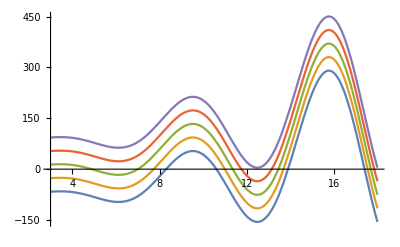

```mathematica
Plot[Evaluate[tab],{x,3,18}]
```

```mathematica
(*?*Plot**)
```

#### Variable Separable equations

```mathematica
DSolve[y'[x]==(x^2 y[x]^2)/(√(3-x^2)),y,x]
```

{{y→({x}↦2/(√(3-x^2) x-3 tan^-1(x/(√(3-x^2)))-2 1))}}

#### Homogeneous equations

```mathematica
eqn=y'[x]==-(x^2-3 y[x]^2)/(x*y[x]);
sol=DSolve[eqn,y,x]
```

{{y→({x}↦-(√(x^2+2 1 x^6))/(√2))},{y→({x}↦(√(x^2+2 1 x^6))/(√2))}}

#### Linear ODE

```mathematica
DSolve[y'[x]+x*y[x]==Exp[3 x],y[x],x]
```

{{y(x)→√(π/2) ⅇ^(-x^2/2-9/2) erfi((x+3)/(√2))+1 ⅇ^(-x^2/2)}}

```mathematica
(*RegionPlot[{ 0.09<Ωrelicsimp[mχ*10^-3,Yχϕ,10*mχ*10^-3,60*mχ*10^-3,0.5*mχ*10^-3,0.1*mχ*10^-3]<0.12,0.09<Ωrelicsimp[mχ*10^-3,Yχϕ,25*mχ*10^-3,60*mχ*10^-3,0.5*mχ*10^-3,0.1*mχ*10^-3]<0.12,0.09<Ωrelicsimp[mχ*10^-3,Yχϕ,50*mχ*10^-3,60*mχ*10^-3,0.5*mχ*10^-3,0.1*mχ*10^-3]<0.12},{mχ,0,500},{Yχϕ,0,0.15},Frame->True,PlotRange->All,ImageSize->800,Epilog->{Text[Style["v_ϕ = 60 m_χ, μ_χ = 0.5 m_χ\n μ_χϕ = 0.1 m_χ",Bold,Black,20],Scaled[{0.3,0.9}]]},PlotStyle->{Directive[Red],Directive[Cyan,Opacity[0.4]],Directive[Yellow,Opacity[0.4]]},PlotPoints->100,FrameLabel->{{HoldForm["Y_χϕ"],None},{HoldForm["m_χ(MeV)"],None}},LabelStyle->{FontFamily->"Times New Roman",30,Black,Bold},Frame-> True,PlotLegends->Placed[SwatchLegend[{Style["m_h_1 = 10 m_χ",20,FontFamily->"Times New Roman"],Style["m_h_1 = 25 m_χ",20,FontFamily->"Times New Roman"],Style["m_h_1 = 50 m_χ",20,FontFamily->"Times New Roman"]},LegendMarkers->Automatic,LegendMarkerSize->20,(*LegendLabel->"Constraints",*)LegendFunction->"Frame"],{0.75,0.225}]]*)
```

#### Bernoulli Equations

```mathematica
sol2=DSolve[y'[x]+4x y[x]==x^3 y[x]^2,y[x],x]
```

{{y(x)→8/(2 x^2+8 1 ⅇ^(2 x^2)+1)}}

## ODE : Numerical Solution

Step 1. Use NDsolve to get the solution of the differential equation 
Step 2. Plot the solution for various values of x

```mathematica
s=NDSolve[{y'[x]==y[x] Cos[x+y[x]],y[0]==1},y,{x,0,30}]
```

{{y→InterpolatingFunction[…]}}

```mathematica
s1=NDSolve[{y'[x]==y[x] Sin[x+45],y[0]==1},y,{x,0,30}]
```

{{y→InterpolatingFunction[…]}}

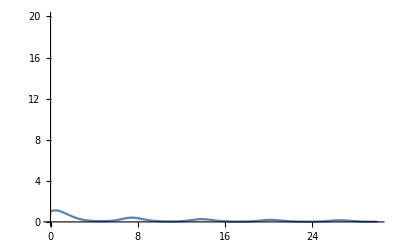

```mathematica
Plot[Evaluate[y[x]/. s],{x,0,30},PlotRange->{{5,10}{0,2}}]
```

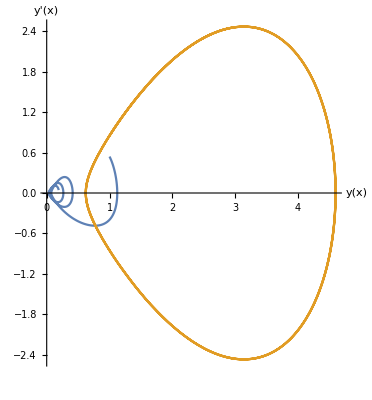

```mathematica
ParametricPlot[{Evaluate[{y[x],y'[x]}/. s],Evaluate[{y[x],y'[x]}/. s1]},{x,0,20},AxesLabel->{Style["y(x)",FontFamily->"Helvetica",Black,FontSize-> 20],"y'(x)"}]
```

## Data handling

```mathematica
nrand=100
```

100

```mathematica
inputlst1=Table[{RandomReal[{1,250}],RandomReal[{0,0.1}]},{nrand}];
inputlst2=Table[{RandomReal[{1,250}],RandomReal[{0.1,0.2}]},{nrand}];
```

```mathematica
inputlst=Join[inputlst1,inputlst2];
```

```mathematica
inputlst;
```

```mathematica
Export["a.m",inputlst];
```

```mathematica
k =Import["a.m"];
```

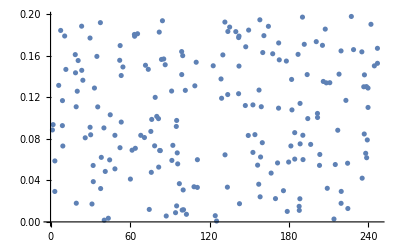

```mathematica
ListPlot[inputlst]
```

```mathematica
f1[x_,y_]=(x^4 y)/(a^2+x^2)/.a->4
```

(x^4 y)/(x^2+16)

```mathematica
Outputlst=#~Join~{f1[Sequence@@#]}&/@k;
```

```mathematica
(*Listcontourplot*)
```